```mathematica
U=({{Cos[Subscript[θ, 12]] Cos[Subscript[θ, 13]], Cos[Subscript[θ, 13]] Sin[Subscript[θ, 12]], ⅇ^(-ⅈ ϕ) Sin[Subscript[θ, 13]]}, {-Cos[Subscript[θ, 23]] Sin[Subscript[θ, 12]]-ⅇ^(ⅈ ϕ) Cos[Subscript[θ, 12]] Sin[Subscript[θ, 13]] Sin[Subscript[θ, 23]], Cos[Subscript[θ, 12]] Cos[Subscript[θ, 23]]-ⅇ^(ⅈ ϕ) Sin[Subscript[θ, 12]] Sin[Subscript[θ, 13]] Sin[Subscript[θ, 23]], Cos[Subscript[θ, 13]] Sin[Subscript[θ, 23]]}, {-ⅇ^(ⅈ ϕ) Cos[Subscript[θ, 12]] Cos[Subscript[θ, 23]] Sin[Subscript[θ, 13]]+Sin[Subscript[θ, 12]] Sin[Subscript[θ, 23]], -ⅇ^(ⅈ ϕ) Cos[Subscript[θ, 23]] Sin[Subscript[θ, 12]] Sin[Subscript[θ, 13]]-Cos[Subscript[θ, 12]] Sin[Subscript[θ, 23]], Cos[Subscript[θ, 13]] Cos[Subscript[θ, 23]]}})
Uc=U/.ϕ->-ϕ;
```

{{Cos[θ_12] Cos[θ_13],Cos[θ_13] Sin[θ_12],ⅇ^(-ⅈ ϕ) Sin[θ_13]},{-Cos[θ_23] Sin[θ_12]-ⅇ^(ⅈ ϕ) Cos[θ_12] Sin[θ_13] Sin[θ_23],Cos[θ_12] Cos[θ_23]-ⅇ^(ⅈ ϕ) Sin[θ_12] Sin[θ_13] Sin[θ_23],Cos[θ_13] Sin[θ_23]},{-ⅇ^(ⅈ ϕ) Cos[θ_12] Cos[θ_23] Sin[θ_13]+Sin[θ_12] Sin[θ_23],-ⅇ^(ⅈ ϕ) Cos[θ_23] Sin[θ_12] Sin[θ_13]-Cos[θ_12] Sin[θ_23],Cos[θ_13] Cos[θ_23]}}

## P_eα(E_ν) curve

```mathematica
masslist={m1^2,m2^2,m3^2}//.{m1^2->0,m2^2->δm^2+m1^2,m3^2->Δm^2+m1^2,
δm^2->7.4 10^-5 eV^2,Δm^2->2.5 10^-3 eV^2}
MeV=10^6 eV
masslistMeV=masslist/MeV^2
ordering0=Ordering[masslist]
```

{0,0.000074 eV^2,0.0025 eV^2}

1000000 eV

{0,7.4×10^-17,2.5×10^-15}

{1,2,3}

```mathematica
(*
<<xunjielib.m

clear′eV[]
gram=unit′gram;cm=unit′cm
GF=StandardModelGF;
neEarth=(5.5gram/cm^3)/(931 MeV)1/2(*1/2 due to most elements have A=2Z*)
neSun=(150gram/cm^3)/(931 MeV)

GF{neSun,neEarth}*)
```

```mathematica
(*the number below is generated by the above code which involkes the package "xunjielib.m"*)
{GfNeSun,GfNeEarth}={8.094392236243736*^-18,1.4839719099780183*^-19}(*MeV*)
```

{8.09439×10^-18,1.48397×10^-19}

```mathematica
U′mEν[EνinMeV_,U_,GfNe_:GfNeSun(*MeV*)(*see ....solar center density ...*),η_:1]:=Module[{U′m,H,M},
H=1/(2Eν) U.DiagonalMatrix[masslistMeV].U†+η √2 GfNe DiagonalMatrix[{1,0,0}];
MatrixForm[M=2Eν H//.{Eν->EνinMeV (*MeV*)}];
{eigv′m,U′m}=Eigensystem[M];
ordering=Ordering[eigv′m];
R′ordering=ConstantArray[0,{3,3}];
Table[R′ordering⟦ordering⟦i⟧,ordering0⟦i⟧⟧=1,{i,3}];

eigv′m=eigv′m.R′ordering;
U′m=(U′mᵀ).R′ordering;
U′m
]

PeαSolar[EνinMeV_,angles_,α_:"μ",η_:1]:=Module[{U′m},
U′n=U/.angles;
U′m=U′mEν[EνinMeV,U′n,GfNeSun,η];
flavor=α/.{"e"->1,"μ"->2,"τ"->3};
Sum[U′m⟦1,i⟧U′m*⟦1,i⟧U′n⟦flavor,i⟧U′n*⟦flavor,i⟧,{i,3}]//Re
]


PαeSolar[EνinMeV_,angles_,α_,η_:1]:=Module[{U′m},
U′n=U/.angles;
U′m=U′mEν[EνinMeV,U′n,GfNeSun,η];
flavor=α/.{"e"->1,"μ"->2,"τ"->3};
Sum[U′m⟦flavor,i⟧U′m*⟦flavor,i⟧U′n⟦1,i⟧U′n*⟦1,i⟧,{i,3}]//Re
]
```

```mathematica
U/.{Subscript[θ, 12]->33.41°,Subscript[θ, 13]->8.57°,Subscript[θ, 23]->45°,ϕ->0}
```

{{0.825431,0.544478,0.149018},{-0.477311,0.532238,0.699212},{0.301393,-0.648279,0.699212}}

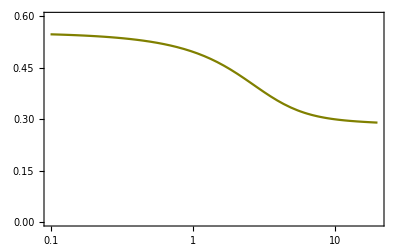
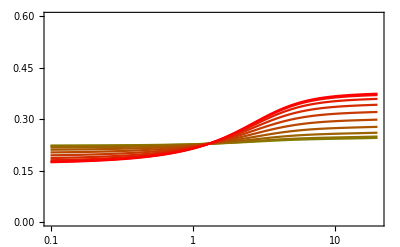
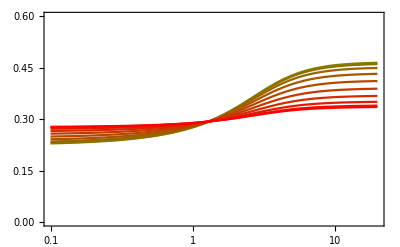

```mathematica
angle={Subscript[θ, 12]->33.41°,Subscript[θ, 13]->8.54°,Subscript[θ, 23]->49.1°,ϕ->0°};
Table[
If[flavor=="e",ϕlist={0},ϕlist=Range[0,180,20]];
Show[
Table[LogLinearPlot[PeαSolar[Eν,Join[angle⟦1;;-2⟧,{ϕ->ϕdegree °}],flavor],{Eν,0.1,20},PlotStyle-> RGBColor[{(ϕdegree+180)/360,(180-ϕdegree)/360,0}]],{ϕdegree,ϕlist}],
PlotRange->{All,{0.0,0.6}},Frame->True,Axes->False],


{flavor,{"e","μ","τ"}}]
```

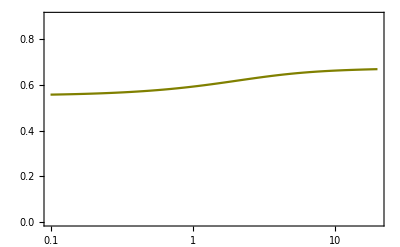
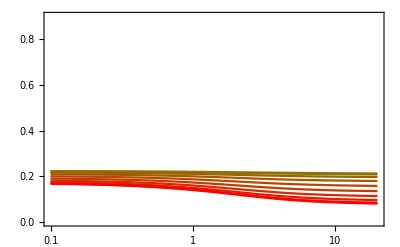
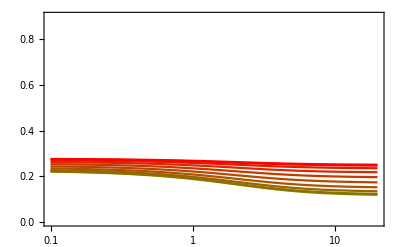

```mathematica
angle={Subscript[θ, 12]->33.41°,Subscript[θ, 13]->8.54°,Subscript[θ, 23]->49.1°,ϕ->0°};
Table[
If[flavor=="e",ϕlist={0},ϕlist=Range[0,180,20]];
Show[
Table[LogLinearPlot[PeαSolar[Eν,Join[angle⟦1;;-2⟧,{ϕ->ϕdegree °}],flavor,(*η*)-1],{Eν,0.1,20},PlotStyle-> RGBColor[{(ϕdegree+180)/360,(180-ϕdegree)/360,0}]],{ϕdegree,ϕlist}],
PlotRange->{All,{0.0,0.9}},Frame->True,Axes->False],


{flavor,{"e","μ","τ"}}]
```

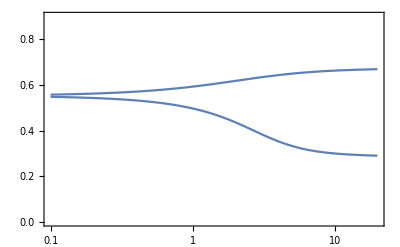

```mathematica
angle={Subscript[θ, 12]->33.41°,Subscript[θ, 13]->8.54°,Subscript[θ, 23]->49.1°,ϕ->0°};
Show[
{
LogLinearPlot[PeαSolar[Eν,angle,"e",(*η*)1],{Eν,0.1,20}],
LogLinearPlot[PeαSolar[Eν,angle,"e",(*η*)-1],{Eν,0.1,20}]
},
PlotRange->{All,{0.0,0.9}},Frame->True,Axes->False]
```

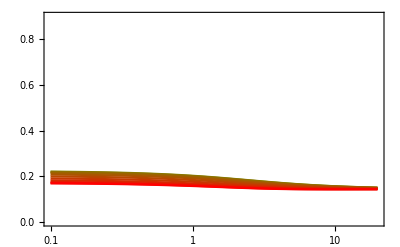
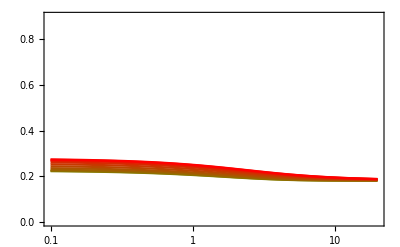
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
angle={Subscript[θ, 12]->33.41°,Subscript[θ, 13]->8.54°,Subscript[θ, 23]->49.1°,ϕ->0°};
Table[
If[flavor=="e",ϕlist={0},ϕlist=Range[0,180,20]];
Show[
Table[LogLinearPlot[PαeSolar[Eν,Join[angle⟦1;;-2⟧,{ϕ->ϕdegree °}],flavor,(*η*)-1],{Eν,0.1,20},PlotStyle-> RGBColor[{(ϕdegree+180)/360,(180-ϕdegree)/360,0}]],{ϕdegree,ϕlist}],
PlotRange->{All,{0.0,0.9}},Frame->True,Axes->False],

{flavor,{"e","μ","τ"}}]
```

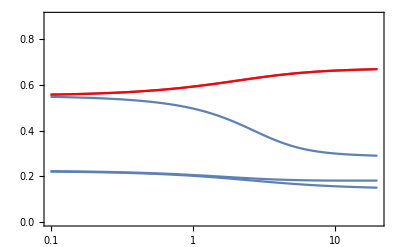

```mathematica
angle={Subscript[θ, 12]->33.41°,Subscript[θ, 13]->8.54°,Subscript[θ, 23]->49.1°,ϕ->0°};
Show[
{
LogLinearPlot[PeαSolar[Eν,angle,"e",(*η*)1],{Eν,0.1,20}],
LogLinearPlot[PeαSolar[Eν,angle,"e",(*η*)-1],{Eν,0.1,20}],
LogLinearPlot[PαeSolar[Eν,angle,"e",(*η*)-1],{Eν,0.1,20},PlotStyle->Red],
LogLinearPlot[PαeSolar[Eν,angle,"μ",(*η*)-1],{Eν,0.1,20}],
LogLinearPlot[PαeSolar[Eν,angle,"τ",(*η*)-1],{Eν,0.1,20}]
},
PlotRange->{All,{0.0,0.9}},Frame->True,Axes->False]
```

```mathematica
Eνlist=Subdivide[0.1,20,100];
data=Table[{Eν,PeαSolar[Eν,angle,"e",(*η*)1],PeαSolar[Eν,angle,"e",(*η*)-1],PαeSolar[Eν,angle,"μ",(*η*)-1],PαeSolar[Eν,angle,"τ",(*η*)-1]},{Eν,Eνlist}];
```

```mathematica
Export[NotebookDirectory[]<>"data/solarP_a_e.dat",data]
```

/home/xj/Dropbox/mywork/solar-vSI/git/code-xunjie/data/solarP_a_e.dat